```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/critical_region/Tc/CL_mub0/buffer

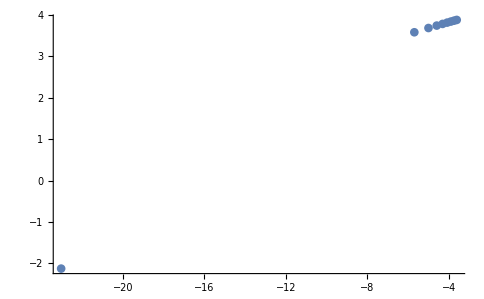

```mathematica
mf=Flatten[Import["./mf.dat"]];
mp=Flatten[Import["./mPion.dat"]];
ms=Flatten[Import["./mSigma.dat"]];
fpi=Flatten[Import["./fpi.dat"]];
Zphi=Flatten[Import["./Zphi.dat"]];
cl=Flatten[Import["./cl.dat"]];
csdata=Transpose[{Log[cl],Log[fpi]}];
ListPlot[csdata,PlotRange->All]
```

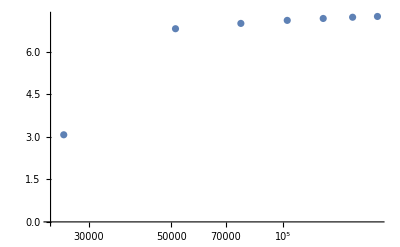

```mathematica
cslogdata=Transpose[{Log[cl*197.33^3],Log[fpi]}];
a1=Table[FindFit[cslogdata[[i-1;;i+1]],a+b x,{a,b},x][[1]][[2]],{i,2,Length[cl]-1}];
b1=Table[FindFit[cslogdata[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[cl]-1}];
ListPlot[Transpose[{cl[[2;;Length[cl]-1]]*197.33^3,1/b1}],ScalingFunctions->{"Log"},PlotRange->All]
```